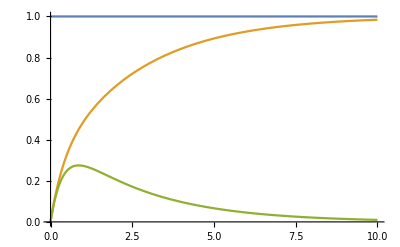

```mathematica
R1=1;
R2=1;
C1=1;
C2=1;
uZ[t]=1;

uzel1=iU[t]==iR1[t];
uzel2=iR1[t]==iC1[t]+iC2[t];
uzel3=iC1[t]==iR2[t];
rovR1=u1[t]-u2[t]==R1*iR1[t];
rovR2=u3[t]==R2*iR2[t];
rovC1=iC1[t]==C1*(u2'[t]-u3'[t]);
rovC2=iC2[t]==C2*u2'[t];
rovU=uZ[t]==u1[t];

podminky={u2[0]==0, u3[0]==0};
rce={uzel1,uzel2,uzel3,rovR1,rovR2,rovR3,rovC1,rovC2,rovU,podminky};
nezname={u1[t], u2[t],u3[t],iC1[t],iC2[t],iU[t],iR1[t],iR2[t]};

vysledek=NDSolve[rce, nezname, {t, 0, 10}];
Plot[Evaluate[{u1[t], u2[t],u3[t]}/.vysledek], {t, 0, 10}]
```